```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/ppmr_fit_table_revreps.csv"}],"csv"];
```

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[4]]
Rsol = R/.LVSS[[4]]
```

-((α Y[M] (kRes (4 (bP[M]-λ[M]+μ[M])^2 (bP[M]+μ[M]+Y[M] ρ[M])+2 (5 bP[M]^2-5 bP[M] λ[M]+2 λ[M]^2+10 bP[M] μ[M]-5 λ[M] μ[M]+5 μ[M]^2+2 Y[M] (bP[M]+μ[M]) ρ[M]) σ[M]+(6 bP[M]-2 λ[M]+6 μ[M]+3 Y[M] ρ[M]) σ[M]^2)+2 bP[M]^2 √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 bP[M] λ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+4 bP[M] μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M]^2 √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 bP[M] Y[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 Y[M] λ[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 Y[M] μ[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 bP[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-Y[M] ρ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))))/(4 σ[M]^2 (2 (λ[M]+Y[M] ρ[M]) (bP[M]+μ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M])))

(kRes (2 (bP[M]-λ[M]+μ[M])+σ[M])+√(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2)))/(4 σ[M])

Metabolic parameters for herbivore consumer

```mathematica
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
```

Metabolic parameters for predator that eats herbivore consumer

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator/prey interaction parameters

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)
(*Parameterizations of the Rohr Model*)

(*palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;*)
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)

(*OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;*)
(*OptPreyMass[Mp_]:=ⅇ^(pbeta/(2 pgamma)) *Mp;*)

(*OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;*)
(*OptPredMass[M_]:=ⅇ^(-pbeta/(2 pgamma)) *M;*)



(*--------------------*)
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=(1+κint)*ppmrint*M^(ppmrslope*(1+κslope));
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)


OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Calculate Herbivore Yield

```mathematica
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

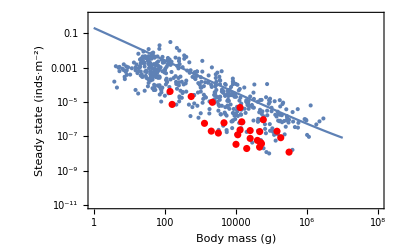

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{bP[M]->0,κint->0,κslope->0},{M,1,10^7},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

Calculate Predator Yield

```mathematica
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
```

Calculate Consumer and Predator Boundary Densities

```mathematica
PreyDensityTheoreticalMax[M_] := YHerbperRes[M]*kRes; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
PreyDensityTheoreticalHalfSat[M_]:=(PreyDensityTheoreticalMax[M]*(1-χ))/χ/.χ->0.99;
PredatorDensityTheoreticalMax[Mp_,M_]:=Ypred[Mp,M]*YHerbperRes[M]*kRes;
```

Calculate per-capita Predation Mortality Rate as (predation rate per gram consumer)*(predated consumer density)

```mathematica
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

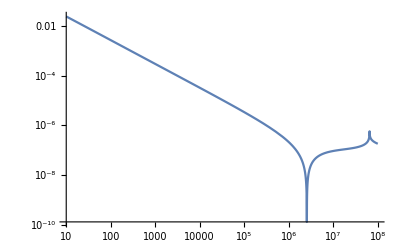

```mathematica
Gensol = (1/M)*Csol/.{κint->0,κslope->0};
LogLogPlot[Abs[Gensol],{M,10,10^8}]
```

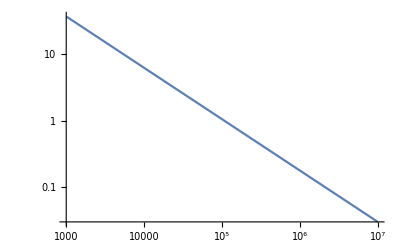

```mathematica
LogLogPlot[(OptPredMass[M]/M)/.{κint->0,κslope->0},{M,10^3,10^7}]
```

```mathematica
MaxConsumerSizePredPreyRatio=Flatten[ParallelTable[Quiet[{i,j,N[(M/.FindMinimum[Abs[(1/M)*Csol/.{κint->i,κslope->j}],M][[2]])]}],{i,-0.99,2,0.01},{j,-0.99,2,0.01}],1];
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratio.csv"}],MaxConsumerSizePredPreyRatio,"CSV"];
```

```mathematica
(*MaxConsumerSizePredPreyRatio=Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratio.csv"}]];*)
```

```mathematica
MaxConsumerSizePredPreyRatioSmall=Flatten[ParallelTable[Quiet[{i,j,N[(M/.FindMinimum[Abs[(1/M)*Csol/.{κint->i,κslope->j}],M][[2]])]}],{i,-0.99,2,0.1},{j,-0.99,2,0.1}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratiosmall.csv"}],MaxConsumerSizePredPreyRatioSmall,"CSV"];
```

```mathematica
Dimensions[MaxConsumerSizePredPreyRatio][[1]]
```

90000

```mathematica
MaxPredatorSizePredPreyRatio=Table[{MaxConsumerSizePredPreyRatio[[i,1]],MaxConsumerSizePredPreyRatio[[i,2]],OptPredMass[MaxConsumerSizePredPreyRatio[[i,3]]]/.{κint->MaxConsumerSizePredPreyRatio[[i,1]],κslope->MaxConsumerSizePredPreyRatio[[i,2]]}},{i,1,Dimensions[MaxConsumerSizePredPreyRatio][[1]]}];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxpredatorsizepredpreyratio.csv"}],MaxPredatorSizePredPreyRatio,"CSV"];
```

```mathematica
MaxPredatorSizePredPreyRatioSmall=Table[{MaxConsumerSizePredPreyRatioSmall[[i,1]],MaxConsumerSizePredPreyRatioSmall[[i,2]],OptPredMass[MaxConsumerSizePredPreyRatioSmall[[i,3]]]/.{κint->MaxConsumerSizePredPreyRatioSmall[[i,1]],κslope->MaxConsumerSizePredPreyRatioSmall[[i,2]]}},{i,1,Dimensions[MaxConsumerSizePredPreyRatioSmall][[1]]}];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxpredatorsizepredpreyratiosmall.csv"}],MaxPredatorSizePredPreyRatioSmall,"CSV"];
```

```mathematica
GraphicsRow[{LD1=ListDensityPlot[MaxConsumerSizePredPreyRatioSmall,PlotLegends->Automatic,ImageSize->300,FrameLabel->{"% Change PPMR Intercept","% Change PPMR Slope"},RegionFunction->Function[{x,y,z},z>1.5*10^6&&z<1.74*10^7]],
LD2=ListDensityPlot[MaxPredatorSizePredPreyRatioSmall,PlotLegends->Automatic,ImageSize->300,FrameLabel->{"% Change PPMR Intercept","% Change PPMR Slope"},RegionFunction->Function[{x,y,z},z>500000&&z<1.2*10^6],ColorFunction->ColorData["SolarColors"]]},ImageSize->800]
```

-Graphics-

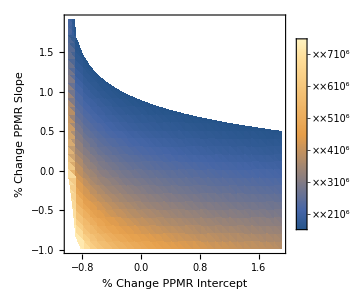
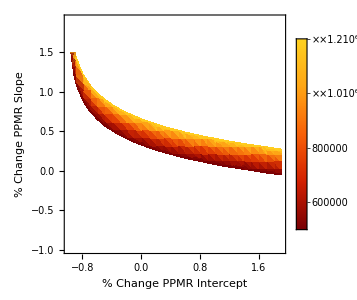

```mathematica
Overlay[{LD1,LD2}]
```

```mathematica
SizePlotPositions =Intersection[Flatten[Position[MaxConsumerSizePredPreyRatio[[All,3]],_?(#>1*10^6&&#<1.74*10^7&)]],Flatten[Position[MaxPredatorSizePredPreyRatio[[All,3]],_?(#>5*10^5&&#<1*10^6 &)]]];
```

```mathematica
PosMaxCarnivoreSize=Position[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]],_?(#==Max[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]&)][[1]][[1]]
```

6220

```mathematica
MaxPredatorSizePredPreyRatio[[SizePlotPositions,All]][[PosMaxCarnivoreSize]]
MaxConsumerSizePredPreyRatio[[SizePlotPositions,All]][[PosMaxCarnivoreSize]]
```

{1.37,0.28,999899.}

{1.37,0.28,1.78946×10^6}

```mathematica
OptPredMass[1.7894563192481543*^6]/.{κint->1.37,κslope->0.28}
```

999899.

```mathematica
MegaMammalPlot=GraphicsRow[{
Show[{
ListDensityPlot[MaxConsumerSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_C^†"],FrameLabel->{"% Change PPMR Intercept","% Change PPMR Slope"}(*,RegionFunction->Function[{x,y,z},z>1.5*10^6&&z<1.74*10^7]*),LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350],
Show[{
ListDensityPlot[MaxPredatorSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_P^†"],FrameLabel->{"% Change PPMR Intercept","% Change PPMR Slope"}(*,RegionFunction->Function[{x,y,z},z>500000&&z<1.2*10^6]*),ColorFunction->ColorData["SolarColors"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350]
},ImageSize->1000]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal.jpg"}],MegaMammalPlot,"JPG",CompressionLevel->0]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal.jpg

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal.pdf"}],MegaMammalPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal.pdf

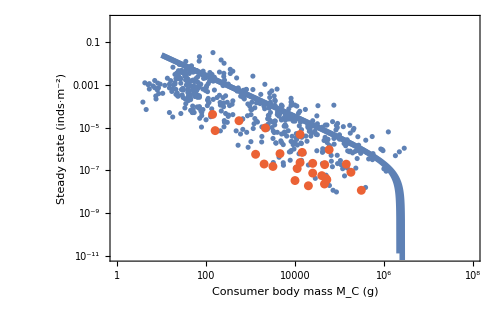

```mathematica
ConsInstabilityPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*Csol/.{κint->0,κslope->0},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,1]}],
LogLogPlot[(1/M)*Csol/.{κint->-0.97,κslope->1.5},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,1]}]
},ImageSize->500]
```

```mathematica
MaxPreyMassSS = M/.FindMinimum[Abs[(1/M)*Csol]/.{κint->-0.97,κslope->1.5},M][[2]]
OptPredMass[MaxPreyMassSS]/.{κint->-0.97,κslope->1.5}
```

2.18727×10^6

422300.